Program calculating rate constants for van der Waals interaction for arbitrary boundary conditions at short range 
Everything in units of R_vdw and E_vdw (characteristic length and energy for van der Waals interaction)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Oem\Desktop\Dipoles final

Parameters:
Lmax - maximal value of angular momentum L
xi - minimal value of r in the grid
nptl - number of points to tabulate the wavelenght
npt - numeber of point per de Broglie wavelenght in the grid 
energ - energy of particles
epsi - small number used to determine initial point of integration
epsf - small number used to determine final point of integration
dxf - step used to determine the final point of integration

Table of parametrs

```mathematica
Lmin=0;Lmax=64;nptl=500;npt=30;epsf=10^-12;epsi=10^-4;dxf=10;
```

```mathematica
KtoEh=3.1668153 10^(-6);
HztoEh=1.519829 10^(-16);
massunit=1.661 10^(-24)/(9.110 10^(-28));
μ=81.25 massunit; 
Debye=0.393456;
d=9/(137*2);
m = 9.18 BohrM;
```

```mathematica
C6=2277;
```

```mathematica
R6=(2 μ C6)^(1/4);E6=1/(2 μ R6^2);
```

```mathematica
abar=(Pi/8)/Gamma[5/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;
C3=2d^2;R3=2 μ C3/R6;E3=(1/(2μ (R6 R3)^2))/E6;
β=R3
```

3.9669

```mathematica
xf=100;
```

```mathematica
freq=30000; 
freqz=0.1 freq;
ω=2 π freq HztoEh; ωz=2 π freqz HztoEh;aHO=(1/Sqrt[μ ω])/R6; aHOz=(1/Sqrt[μ ωz])/R6;
α=(1/aHO)^4;
αz=(1/aHOz)^4;
Ω=2 Sqrt[α];
Ωz=2 Sqrt[αz];
```

Potentials

```mathematica
Vho[l1_,ml1_,l2_,ml2_]:= (If[l1==l2,1,0]If[ml1==ml2,1,0]-(1-αz/α)If[ml1==ml2,1,0]/3((-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1] 2 ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}] + If[l1==l2,1,0]));
Vedd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];(*Dodać symbol wignera*)
Vmdd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];
Vvdw[l1_,ml1_,l2_,ml2_]:= -If[l1==l2,1,0]If[ml1==ml2,1,0];
```

```mathematica
Veddtab=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vmddtab=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vvdwtab=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vhotab=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vcftab = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,0,Lmax},{l2,0,Lmax}]]];
Veddtab2=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vmddtab2=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vvdwtab2=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vhotab2=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vcftab2 = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,1,Lmax},{l2,1,Lmax}]]];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
Vhotable[x_]:=N[(Table[Vhotab[[l1/2+1,l2/2+1]],{l1,0,Lmax},{l2,0,Lmax}])/.{r->x}];
```

Table of channels

```mathematica
TabCh={};Do[AppendTo[TabCh,{l(*,m*)}],{l,Lmin,Lmax}(*,{m,-l,l}*)];Nch=Length[TabCh];Id=IdentityMatrix[Lmax+1];Nch
```

65

Spherical Bessel functions

```mathematica
jl[l_,x_]:=Sqrt[Pi/(2x)]BesselJ[l+1/2,x];nl[l_,x_]:=(-1)^(l+1) Sqrt[Pi/(2x)]BesselJ[-l-1/2,x]
```

Matrix containg potential

```mathematica
V[r_]:=1/r^2 Vcftab + 1/r^6 Vvdwtab +β/r^3 Veddtab;
```

```mathematica
Length[V[1][[1]]]
```

65

Adiabatic potentials (diagonalized V[r]) + van der Waals potential

```mathematica
(*LogLinearPlot[{(Take[Sort[Eigenvalues[V[x]]],Lmax/2+1]),(Take[Sort[Eigenvalues[V2[x]]],Lmax/2])},{x,0.5,xf},
PlotRange->Automatic,AxesOrigin->{0.5,0},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},PlotLegends->Placed[LineLegend[{Style["Bosonic",FontFamily->"Times",FontWeight->Bold],Style["Fermionic",FontFamily->"Times",FontWeight->Bold]}, LegendLabel->Style["Collision channels",FontSize->14, FontFamily->"Times",FontWeight->Bold],LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMargins->5],{Left,Top}],FrameLabel->{Style["r (R_vdW)",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["Adiabatic energies (E_ω)",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]*)
```

```mathematica
N[abar]*4
```

1.91196

Short range solution for van der Waals potential, with the short range phase "phi"

```mathematica
sol0[r_,A_,B_]=A Sqrt[r]BesselJ[1/4,1/(2 r^2)]+B Sqrt[r] BesselY[1/4,1/(2 r^2)];
```

```mathematica
ash[phi_]:=abar (1+Tan[phi])
```

```mathematica
as[y_,s_]:=abar(s+y(1+(1-s)^2)/(ⅈ+y(1-s)));
ap[y_,s_,k_]:=-2 abar1  (k abar)^2  (y+ⅈ(s-1))/(y s+ⅈ(s-2))
```

Table of short range solutions

```mathematica
Psi0[r_,A_,B_]:=Table[If[n1==n2,sol0[r,A,B],0] ,{n1,1,Nch},{n2,1,Nch}]
```

Subroutine performing outward integration using renormalized Numerov method
It takes Psi0 as an initial condition

Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
phi - short-range phase

```mathematica
evolNumOut[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,A_?NumericQ,B_?NumericQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,Ro,Rprod},

nodes=0;

Rout[n0]=Psi0[xt[[n0+1]],A,B].Inverse[Psi0[xt[[n0]],A,B]];
h=xt[[n0+1]]-xt[[n0]];
n=n0+1;

While[n<=nf,
h0=h;
h=xt[[n+1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n-2]]).Inverse[Rout[n-1].Rout[n-2]]);,

Abs[h]<0.75 Abs[h0],
Qt=en Id-V[(xt[[n]]+xt[[n-1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n-1]]).Inverse[Rout[n-1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n-1]]).Inverse[Rout[n-1]]);
];
n++;
];
Ro=Rout[nf];
Rprod=Inverse[Rout[n0]];Do[Rprod=Rprod.Inverse[Rout[n]],{n,n0+1,nf-1}];
Clear[W,n,Rinv,h,h0,Qt];
If[cl==1,Clear[Rout]];
{Ro,Rprod}]
```

Subroutine calculating K matrix

Parameters:
en -  the energy
A,B - constants determining boundary conditions at short range 

Output:
K matrix

```mathematica
KMatrix[en_?NumericQ,A_?NumericQ,B_?NumericQ]:=
Module[{J1,J2,N1,N2,Rn,K,r1,r2,kv,n1,n2,Rprod,R},
R=evolNumOut[en,1,nstep-1,A,B,1];
Rn=R[[1]];
kv=Sqrt[en];
r1=xt[[nstep-1]];
r2=xt[[nstep]];
J1=Table[If[n1==n2, kv r1 jl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
J2=Table[If[n1==n2,kv r2 jl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
N1=Table[If[n1==n2,kv r1 nl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
N2=Table[If[n1==n2,kv r2 nl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
K=-Inverse[Rn.N1-N2].(J2-Rn.J1);
K];
```

Subroutine calculating K and T matrices

Parameters:
en -  the energy
A,B - constants determining boundary conditions at short range 

Output:
K matrix
T matrix

```mathematica
KCTMatrix[en_?NumericQ,A_?NumericQ,B_?NumericQ]:=
Module[{J1,J2,N1,N2,Rn,K,r1,r2,kv,n1,n2,Rprod,R,W,T},
R=evolNumOut[en,1,nstep-1,A,B,1];
Rn=R[[1]];
Rprod=R[[2]];
kv=Sqrt[en];
r1=xt[[nstep-1]];
r2=xt[[nstep]];
J1=Table[If[n1==n2, kv r1 jl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
J2=Table[If[n1==n2,kv r2 jl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
N1=Table[If[n1==n2,kv r1 nl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
N2=Table[If[n1==n2,kv r2 nl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
K=-Inverse[Rn.N1-N2].(J2-Rn.J1);
W=Rprod.(J1+N1.K).Inverse[Id-ⅈ K];
R=ConjugateTranspose[W].W;
W=Inverse[Id-ⅈ K];
T=W.K/ Sqrt[en];
{T,K,Re[Tr[R]]}];
```

```mathematica
yy=0;ss=4.;
```

```mathematica
aS=as[yy,ss]
```

1.91196+0. ⅈ

```mathematica
aP=ap[yy,ss,Sqrt[en]]
```

(-0.348683+0. ⅈ) en

```mathematica
phi=φ/.Solve[aS==ash[φ],φ][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.24905

```mathematica
abar=(Pi/8)/Gamma[5/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;
```

energies

```mathematica
en0=0.0001;enf=100.;de=(Log[enf]-Log[en0])/50;
```

```mathematica
TabEn=Table[Exp[ee],{ee,Log[en0],Log[enf],de}]
```

{0.0001,0.000131826,0.00017378,0.000229087,0.000301995,0.000398107,0.000524807,0.000691831,0.000912011,0.00120226,0.00158489,0.0020893,0.00275423,0.00363078,0.0047863,0.00630957,0.00831764,0.0109648,0.0144544,0.0190546,0.0251189,0.0331131,0.0436516,0.057544,0.0758578,0.1,0.131826,0.17378,0.229087,0.301995,0.398107,0.524807,0.691831,0.912011,1.20226,1.58489,2.0893,2.75423,3.63078,4.7863,6.30957,8.31764,10.9648,14.4544,19.0546,25.1189,33.1131,43.6516,57.544,75.8578,100.}

loop

```mathematica
Elastic={};Inelastic={}; Sections={};
Print["Progress:"];
Print[ProgressIndicator[Dynamic[counter],{1,Length[TabEn]}]];
Do[en=TabEn[[i]];
counter=i;
(*Print["en = ",en];*)

xi=0.28;
(*Determines the final point of integration*)
xf=100;

(* Subroutine determining steps *)
Module[{eig,h,dbl,n,pxi,pxf,dp,x,p,tab},

pxi=Log[xi ];
pxf=Log[xf +dxf];
dp=(pxf-pxi)/nptl;
tab=Table[x=Exp[p];eig=Eigenvalues[V[x]];{x,Min[2Pi/Sqrt[Abs[en-eig]]]},{p,pxi,pxf,dp}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,


AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
];
(*Print["nstep = ",nstep];*)
QT=Table[en Id-V[xt[[n]]],{n,1,Length[xt]}];
Kmatr=KMatrix[en,Sin[phi],Cos[phi]];
Smatr=(Id+ⅈ Kmatr).Inverse[Id-ⅈ Kmatr];
S0 = N[Smatr[[1,1]]];
a0 = 1/(ⅈ Sqrt[en])(1-S0)/(1+S0);

(*totinelS=Pi Sum[1-Abs[Smatr[[n1,n1]]]^2,{n1,1,1}]/en;
totelS=Pi Sum[Abs[1-Smatr[[n1,n1]]]^2,{n1,1,1}]/en;*)

totInEl= Sum[(2TabCh[[n1,1]]+1)(1-Abs[Smatr[[n1,n1]]]^2),{n1,1,Nch}];
totEl=  Sum[(2TabCh[[n1,1]]+1)Abs[1-Smatr[[n1,n1]]]^2,{n1,1,Nch}];

AppendTo[Elastic,{en,totEl}];
AppendTo[Inelastic,{en,totInEl}];
AppendTo[Sections,{en,a0}];

Clear[xt,QT];
,{i,1,Length[TabEn]}
]
```

Progress:

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00284479,0.,0.0000862194,0.,2.40302×10^-6,0.,1.26261×10^-7,0.,7.86183×10^-9,0.,«55»},{0.,-0.00789072,0.,0.000165545,0.,3.91574×10^-6,0.,1.82194×10^-7,0.,1.03434×10^-8,«55»},{0.0000129202,0.,-0.038518,0.,0.000715134,0.,0.0000151942,0.,6.51864×10^-7,0.,«55»},{0.,0.0000136759,0.,-0.266038,0.,0.00467534,0.,0.0000927095,0.,3.7644×10^-6,«55»},{1.144×10^-8,0.,0.000022719,0.,-2.37583,0.,0.0404935,0.,0.000765056,0.,«55»},{0.,5.36107×10^-9,0.,0.0000774836,0.,-26.0123,0.,0.43501,0.,0.00792857,«55»},{6.20757×10^-12,0.,4.98499×10^-9,0.,0.000418183,0.,-337.21,0.,5.56894,0.,«55»},{0.,1.76677×10^-12,0.,1.08825×10^-8,0.,0.0030811,0.,-5050.03,0.,82.685,«55»},{1.9974×10^-15,0.,1.10517×10^-12,0.,4.08283×10^-8,0.,0.0287778,0.,-85783.3,0.,«55»},{0.,3.95125×10^-16,0.,1.74071×10^-12,0.,2.21221×10^-7,0.,0.325723,0.,-1.62957×10^6,«55»},«55»} may contain significant numerical errors.

General::munfl: (2.08765×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.03649×10^-161)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.90366×10^-165)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00300914,0.,0.0000724848,0.,1.50229×10^-6,0.,5.96205×10^-8,0.,2.81022×10^-9,0.,«55»},{0.,-0.00710006,0.,0.000115258,0.,2.05898×10^-6,0.,7.25984×10^-8,0.,3.12457×10^-9,«55»},{0.0000102545,0.,-0.0298992,0.,0.000425366,0.,6.85471×10^-6,0.,2.23081×10^-7,0.,«55»},{0.,0.0000127864,0.,-0.178926,0.,0.00240021,0.,0.0000361337,0.,1.11337×10^-6,«55»},{9.23717×10^-9,0.,0.0000184874,0.,-1.38714,0.,0.0180111,0.,0.000258398,0.,«55»},{0.,5.07491×10^-9,0.,0.0000533267,0.,-13.1978,0.,0.167947,0.,0.00232436,«55»},{5.03537×10^-12,0.,4.09217×10^-9,0.,0.000247394,0.,-148.767,0.,1.86814,0.,«55»},{0.,1.68023×10^-12,0.,7.53829×10^-9,0.,0.00157702,0.,-1938.,0.,24.1157,«55»},{1.62323×10^-15,0.,9.10815×10^-13,0.,2.42739×10^-8,0.,0.0127764,0.,-28644.,0.,«55»},{0.,3.76641×10^-16,0.,1.20974×10^-12,0.,1.13674×10^-7,0.,0.1256,0.,-473539.,«55»},«55»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00324737,0.,0.0000630255,0.,9.67047×10^-7,0.,2.89362×10^-8,0.,1.03169×10^-9,0.,«55»},{0.,-0.0064589,0.,0.0000817487,0.,1.10016×10^-6,0.,2.93826×10^-8,0.,9.58486×10^-10,«55»},{6.659×10^-6,0.,-0.023384,0.,0.000255844,0.,3.12601×10^-6,0.,7.71676×10^-8,0.,«55»},{0.,0.0000119472,0.,-0.121033,0.,0.00124196,0.,0.0000141972,0.,3.31987×10^-7,«55»},{6.13557×10^-9,0.,0.0000153634,0.,-0.813675,0.,0.00806014,0.,0.0000878331,0.,«55»},{0.,4.82028×10^-9,0.,0.0000372339,0.,-6.72251,0.,0.0651627,0.,0.000685012,«55»},{3.36472×10^-12,0.,3.44035×10^-9,0.,0.00014772,0.,-65.855,0.,0.6293,0.,«55»},{0.,1.60568×10^-12,0.,5.30865×10^-9,0.,0.000812736,0.,-745.958,0.,7.05885,«55»},{1.08728×10^-15,0.,7.6972×10^-13,0.,1.45895×10^-8,0.,0.00570349,0.,-9590.13,0.,«55»},{0.,3.61024×10^-16,0.,8.55626×10^-13,0.,5.88881×10^-8,0.,0.0486532,0.,-137939.,«55»},«55»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{0.0001,6.40912×10^-6},{0.000131826,0.0000136436},{0.00017378,0.0000283892},{0.000229087,0.0000573486},{0.000301995,0.000111512},{0.000398107,0.000206542},{0.000524807,0.000359988},{0.000691831,0.000582861},{0.000912011,0.00086729},{0.00120226,0.00118252},{0.00158489,0.00149749},{0.0020893,0.00182732},{0.00275423,0.00226249},{0.00363078,0.00292359},{0.0047863,0.00380477},{0.00630957,0.00484185},{0.00831764,0.00623463},{0.0109648,0.00811617},{0.0144544,0.0104892},{0.0190546,0.0136872},{0.0251189,0.017819},{0.0331131,0.0232184},{0.0436516,0.0302808},{0.057544,0.0394243},{0.0758578,0.0511946},{0.1,0.066223},{0.131826,0.0851456},{0.17378,0.108599},{0.229087,0.13699},{0.301995,0.170308},{0.398107,0.207701},{0.524807,0.246997},{0.691831,0.284198},{0.912011,0.313241},{1.20226,0.32677},{1.58489,0.319222},{2.0893,0.295213},{2.75423,0.28864},{3.63078,0.399322},{4.7863,0.834574},{6.30957,1.84066},{8.31764,3.32432},{10.9648,4.64261},{14.4544,5.40787},{19.0546,5.96684},{25.1189,6.66201},{33.1131,7.37546},{43.6516,8.81095},{57.544,9.01738},{75.8578,9.6883},{100.,10.3036}}

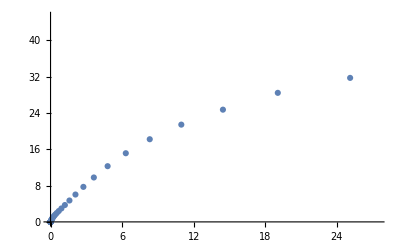

```mathematica
Inelastic
ListPlot[Elastic]
```

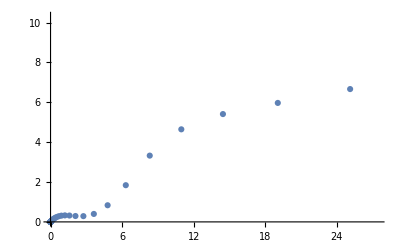

```mathematica
ListPlot[Inelastic]
```

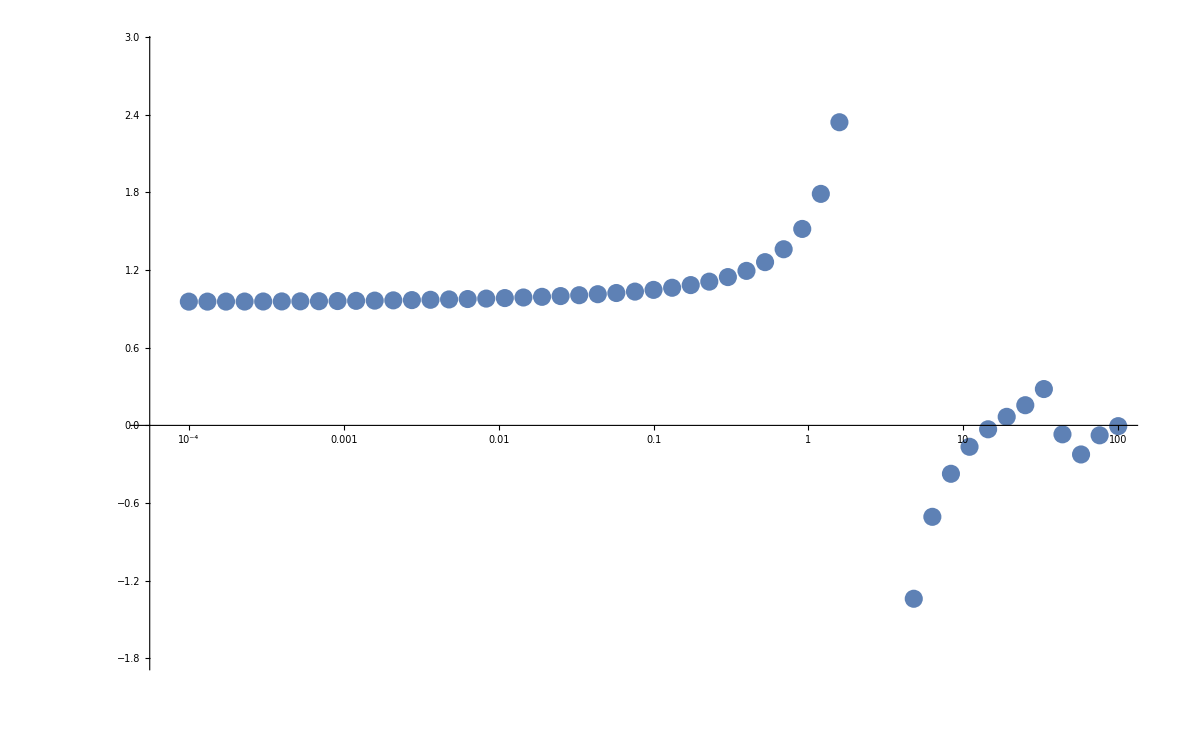

```mathematica
ListLogLinearPlot[Re[Sections]]
```

```mathematica
Re[Sections]
```

{{0.0001,0.956156},{0.000131826,0.956324},{0.00017378,0.956543},{0.000229087,0.956832},{0.000301995,0.957218},{0.000398107,0.957741},{0.000524807,0.958456},{0.000691831,0.959425},{0.000912011,0.960688},{0.00120226,0.962236},{0.00158489,0.964003},{0.0020893,0.96592},{0.00275423,0.968001},{0.00363078,0.970371},{0.0047863,0.973141},{0.00630957,0.976258},{0.00831764,0.97971},{0.0109648,0.983674},{0.0144544,0.988132},{0.0190546,0.993225},{0.0251189,0.999029},{0.0331131,1.00573},{0.0436516,1.01353},{0.057544,1.0227},{0.0758578,1.03364},{0.1,1.04691},{0.131826,1.0633},{0.17378,1.08395},{0.229087,1.11058},{0.301995,1.14579},{0.398107,1.19371},{0.524807,1.26126},{0.691831,1.36084},{0.912011,1.51782},{1.20226,1.78861},{1.58489,2.342},{2.0893,3.98476},{2.75423,66.1059},{3.63078,-3.28284},{4.7863,-1.33924},{6.30957,-0.706293},{8.31764,-0.373824},{10.9648,-0.165251},{14.4544,-0.0300797},{19.0546,0.0660925},{25.1189,0.155974},{33.1131,0.280835},{43.6516,-0.0689364},{57.544,-0.224597},{75.8578,-0.0765803},{100.,-0.00583005}}

Imports

```mathematica
imported = Import["Drop_3D_30_07.csv"];
imported=Sort[imported,#1[[1]]<#2[[1]]&];
scat=Transpose[imported][[1]];
scat = (1/aHOz)*scat;
scat=1/scat;

energies=Transpose[imported][[2]];
energies = Ωz * energies;

colored = Join[Transpose[imported], {Range[Length[scat]]}];
```

```mathematica
Export["Before_scat_colored.csv",Transpose[colored]]
```

Before_scat_colored.csv

Calculations

```mathematica
Elastic={};Inelastic={}; Sections={};Scattered={}; Sections1D={};
en = 0.0000001;
Print["Progress:"];
Print[ProgressIndicator[Dynamic[k],{1,Length[scat]}]];
Do[aS=scat[[i]];
k=i;
(*Print["as = ",aS];*)

xi=0.28;
(*Determines the final point of integration*)
xf=100;

(* Subroutine determining steps *)
Module[{eig,h,dbl,n,pxi,pxf,dp,x,p,tab},

pxi=Log[xi ];
pxf=Log[xf +dxf];
dp=(pxf-pxi)/nptl;
tab=Table[x=Exp[p];eig=Eigenvalues[V[x]];{x,Min[2Pi/Sqrt[Abs[en-eig]]]},{p,pxi,pxf,dp}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,


AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
];
(*Print["nstep = ",nstep];*)
QT=Table[en Id-V[xt[[n]]],{n,1,Length[xt]}];
phi=φ/.Solve[aS==ash[φ],φ][[1]];
Kmatr=KMatrix[en,Sin[phi],Cos[phi]];
Smatr=(Id+ⅈ Kmatr).Inverse[Id-ⅈ Kmatr];
S0 = N[Smatr[[1,1]]];
a0 = 1/(ⅈ Sqrt[en])(1-S0)/(1+S0);

(*totinelS=Pi Sum[1-Abs[Smatr[[n1,n1]]]^2,{n1,1,1}]/en;
totelS=Pi Sum[Abs[1-Smatr[[n1,n1]]]^2,{n1,1,1}]/en;*)
(*Print[a0];*)
totInEl= Sum[(2TabCh[[n1,1]]+1)(1-Abs[Smatr[[n1,n1]]]^2),{n1,1,Nch}];
totEl=  Sum[(2TabCh[[n1,1]]+1)Abs[1-Smatr[[n1,n1]]]^2,{n1,1,Nch}];

AppendTo[Elastic,{en,totEl}];
AppendTo[Inelastic,{en,totInEl}];
AppendTo[Sections,Re[a0]];
AppendTo[Sections1D,i];
AppendTo[Scattered,{aS,Re[a0]}];

Clear[xt,QT];
,{i,1,Length[scat]}
]
```

Progress:

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00234613,0.,0.0650871,0.,1.96715,0.,106.148,0.,6723.41,0.,«55»},{0.,-0.225809,0.,4.47636,0.,106.851,0.,4985.36,0.,283537.,«55»},{0.0000215825,0.,-35.86,0.,646.066,0.,13718.9,0.,588483.,0.,«55»},{0.,0.000297182,0.,-7958.6,0.,137236.,0.,2.7136×10^6,0.,1.10052×10^8,«55»},{1.85539×10^-8,0.,0.0183766,0.,-2.27048×10^6,0.,3.81938×10^7,0.,7.19245×10^8,0.,«55»},{0.,1.12092×10^-7,0.,2.16852,0.,-7.91638×10^8,0.,1.3112×10^10,0.,2.38223×10^11,«55»},{1.00671×10^-11,0.,3.92375×10^-6,0.,384.047,0.,-3.26195×10^11,0.,5.34754×10^12,0.,«55»},{0.,3.64066×10^-11,0.,0.00029849,0.,91276.1,0.,-1.55086×10^14,0.,2.52454×10^15,«55»},{3.25516×10^-15,0.,8.59223×10^-10,0.,0.0369196,0.,2.72986×10^7,0.,-8.35648×10^16,0.,«55»},{0.,8.08309×10^-15,0.,4.72568×10^-8,0.,6.47371,0.,9.85511×10^9,0.,-5.03245×10^19,«55»},«55»} may contain significant numerical errors.

General::munfl: (1.44545×10^-160)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.27582×10^-167)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.18181×10^-173)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.0023461,0.,0.0650879,0.,1.9672,0.,106.152,0.,6723.67,0.,«55»},{0.,-0.225809,0.,4.47636,0.,106.851,0.,4985.36,0.,283537.,«55»},{0.0000215827,0.,-35.86,0.,646.066,0.,13718.9,0.,588483.,0.,«55»},{0.,0.000297182,0.,-7958.6,0.,137236.,0.,2.7136×10^6,0.,1.10052×10^8,«55»},{1.85543×10^-8,0.,0.0183766,0.,-2.27048×10^6,0.,3.81938×10^7,0.,7.19245×10^8,0.,«55»},{0.,1.12092×10^-7,0.,2.16852,0.,-7.91638×10^8,0.,1.3112×10^10,0.,2.38223×10^11,«55»},{1.00674×10^-11,0.,3.92375×10^-6,0.,384.047,0.,-3.26195×10^11,0.,5.34754×10^12,0.,«55»},{0.,3.64066×10^-11,0.,0.00029849,0.,91276.1,0.,-1.55086×10^14,0.,2.52454×10^15,«55»},{3.25528×10^-15,0.,8.59223×10^-10,0.,0.0369196,0.,2.72986×10^7,0.,-8.35648×10^16,0.,«55»},{0.,8.08309×10^-15,0.,4.72568×10^-8,0.,6.47371,0.,9.85511×10^9,0.,-5.03245×10^19,«55»},«55»} may contain significant numerical errors.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00234593,0.,0.0650926,0.,1.96748,0.,106.171,0.,6725.1,0.,«55»},{0.,-0.225809,0.,4.47636,0.,106.851,0.,4985.36,0.,283537.,«55»},{0.0000215843,0.,-35.86,0.,646.066,0.,13718.9,0.,588483.,0.,«55»},{0.,0.000297182,0.,-7958.6,0.,137236.,0.,2.7136×10^6,0.,1.10052×10^8,«55»},{1.8557×10^-8,0.,0.0183766,0.,-2.27048×10^6,0.,3.81938×10^7,0.,7.19245×10^8,0.,«55»},{0.,1.12092×10^-7,0.,2.16852,0.,-7.91638×10^8,0.,1.3112×10^10,0.,2.38223×10^11,«55»},{1.00693×10^-11,0.,3.92375×10^-6,0.,384.047,0.,-3.26195×10^11,0.,5.34754×10^12,0.,«55»},{0.,3.64066×10^-11,0.,0.00029849,0.,91276.1,0.,-1.55086×10^14,0.,2.52454×10^15,«55»},{3.25597×10^-15,0.,8.59223×10^-10,0.,0.0369196,0.,2.72986×10^7,0.,-8.35648×10^16,0.,«55»},{0.,8.08309×10^-15,0.,4.72568×10^-8,0.,6.47371,0.,9.85511×10^9,0.,-5.03245×10^19,«55»},«55»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

```mathematica
Spectral=Join[{aHOz/Sections},{energies/Ωz}];
Spectral1=Join[{aHOz/Sections},{energies/Ωz},{Sections1D}];
Spectral1=Transpose[Spectral1];
Spectral=Transpose[Spectral];
Spectral
```

```mathematica
Export["Spectral_02.csv",Spectral];
Export["Spectral_colored.csv",Spectral1];
```

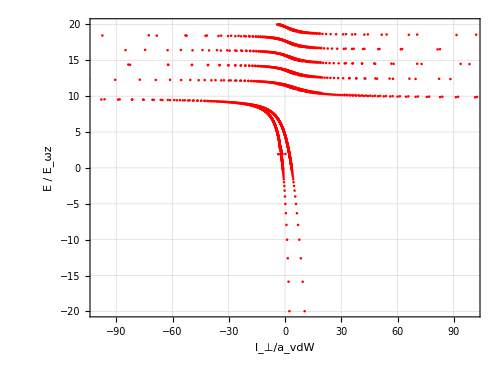

```mathematica
ListPlot[Re[Spectral],PlotRange->{{-100,100},All},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
Spectral
```

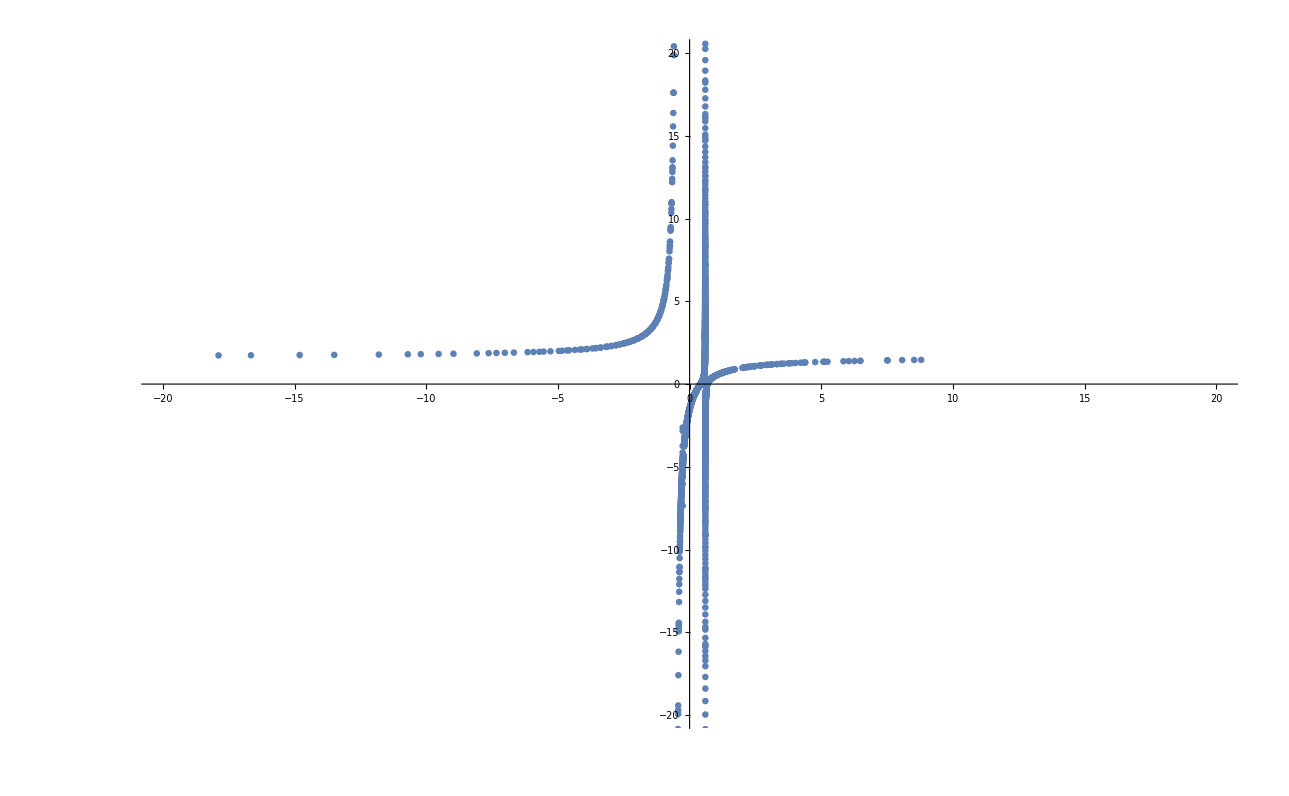

Scattered_02.csv

```mathematica
ListPlot[Re[Scattered], PlotRange->{{-20,20},{-20,20}}]
Export["Scattered_02.csv",Scattered]
```

```mathematica
Sections
```

{-1.50001,-1.50132,-1.5088,-1.51071,-1.51629,-1.52379,-1.53131,-1.53553,-1.53883,-1.54086,-1.54637,-1.55391,-1.56147,-1.56904,-1.57662,-1.58421,-1.59182,-1.59943,-1.60005,-1.60706,-1.61303,-1.6147,-1.62235,-1.63001,-1.63769,-1.63947,-1.64337,-1.64538,-1.65308,-1.66079,-1.66852,-1.67626,-1.68401,-1.69177,-1.69955,-1.70729,-1.70735,-1.71515,-1.72216,-1.72297,-1.73081,-1.73865,-1.74651,-1.74982,-1.75439,-1.75443,-1.76228,-1.77018,-1.7781,-1.78604,-1.79399,-1.80195,-1.80993,-1.81792,-1.82265,-1.82593,-1.83395,-1.83893,-1.84199,-1.85005,-1.85812,-1.8662,-1.86731,-1.87431,-1.87531,-1.88243,-1.89056,-1.89871,-1.90688,-1.91506,-1.92326,-1.93148,-1.93972,-1.94724,-1.94797,-1.95624,-1.96433,-1.96452,-1.97283,-1.98115,-1.98949,-1.9928,-1.99784,-2.00622,-2.0075,-2.01461,-2.02302,-2.03145,-2.0399,-2.04836,-2.05685,-2.06535,-2.07387,-2.08235,-2.08241,-2.09097,-2.09947,-2.09955,-2.10815,-2.11677,-2.12541,-2.12728,-2.13406,-2.14274,-2.15144,-2.15281,-2.16015,-2.16889,-2.17765,-2.18643,-2.19523,-2.20405,-2.21289,-2.22175,-2.2295,-2.23063,-2.23954,-2.24566,-2.24846,-2.25741,-2.26638,-2.27185,-2.27537,-2.28438,-2.29341,-2.30247,-2.31155,-2.31339,-2.32065,-2.32977,-2.33891,-2.34808,-2.35727,-2.36648,-2.37572,-2.38498,-2.39045,-2.39426,-2.40357,-2.40439,-2.41289,-2.42225,-2.42775,-2.43162,-2.44102,-2.45045,-2.45989,-2.46937,-2.47886,-2.48838,-2.4918,-2.49792,-2.50749,-2.51709,-2.5267,-2.53635,-2.54601,-2.5557,-2.56542,-2.56722,-2.57516,-2.5773,-2.58493,-2.59472,-2.5963,-2.60454,-2.61438,-2.62425,-2.63414,-2.64406,-2.654,-2.66397,-2.67397,-2.68399,-2.69098,-2.69403,-2.70411,-2.7142,-2.72433,-2.73448,-2.74465,-2.75485,-2.76193,-2.76508,-2.76605,-2.77533,-2.77876,-2.7856,-2.79591,-2.80624,-2.81659,-2.82697,-2.83737,-2.8478,-2.85825,-2.86873,-2.87924,-2.88977,-2.90032,-2.91089,-2.91385,-2.9215,-2.93212,-2.94277,-2.95344,-2.96413,-2.97175,-2.97485,-2.9757,-2.97626,-2.98559,-2.99635,-3.00713,-3.01794,-3.02876,-3.03961,-3.05047,-3.06136,-3.07226,-3.08318,-3.09411,-3.10507,-3.11603,-3.12702,-3.13801,-3.14902,-3.16004,-3.16144,-3.17107,-3.18211,-3.18518,-3.19289,-3.19316,-3.20422,-3.2091,-3.21528,-3.22634,-3.23741,-3.24848,-3.25954,-3.27061,-3.28166,-3.29271,-3.29934,-3.30375,-3.31478,-3.32579,-3.33678,-3.34775,-3.3587,-3.36962,-3.38051,-3.39136,-3.39574,-3.40218,-3.41295,-3.4171,-3.42324,-3.42367,-3.43434,-3.44496,-3.44635,-3.45551,-3.466,-3.47641,-3.47876,-3.48675,-3.497,-3.50716,-3.51722,-3.52719,-3.53704,-3.54677,-3.55639,-3.56587,-3.56926,-3.57521,-3.58442,-3.59347,-3.59884,-3.60237,-3.60269,-3.6111,-3.61967,-3.62806,-3.63244,-3.63627,-3.63993,-3.6443,-3.65213,-3.65978,-3.66723,-3.67448,-3.68153,-3.68838,-3.69503,-3.70148,-3.70772,-3.71376,-3.71961,-3.72526,-3.73072,-3.73599,-3.74107,-3.74597,-3.7507,-3.75525,-3.75964,-4.2744,-4.33131,-4.34265,-4.34469,-4.35837,-4.37236,-4.38617,-4.38666,-4.40128,-4.41622,-4.43149,-4.4359,-4.4471,-4.46305,-4.47681,-4.47937,-4.49606,-4.51314,-4.53064,-4.54858,-4.56698,-4.5859,-4.60536,-4.62543,-4.64617,-4.66766,-4.69,-4.7133,-4.73772,-4.76346,-4.79076,-4.81996,-4.84212,-4.8515,-4.88597,-4.92422,-4.96747,-5.01756,-5.07739,-5.1518,-5.24958,-5.32442,-5.38837,-5.60983,-6.04129,-7.34885,38.3823,-2.62701,-2.82808,-3.7391,-4.135,-4.34467,-4.47872,-4.49478,-4.57466,-4.64876,-4.7092,-4.76054,-4.76779,-4.80553,-4.84594,-4.88292,-4.9173,-4.93234,-4.94966,-4.98042,-5.00991,-5.03837,-5.066,-5.09294,-5.11931,-5.14523,-5.17075,-5.19596,-5.20783,-5.22091,-5.24565,-5.27021,-5.29462,-5.31893,-5.34315,-5.35602,-5.36731,-5.39142,-5.40305,-5.41551,-5.43062,-5.43958,-5.46366,-5.48775,-5.51186,-5.53601,-5.5602,-5.58444,-5.60854,-5.60874,-5.63311,-5.65755,-5.68206,-5.70666,-5.73135,-5.75612,-5.781,-5.80598,-5.83106,-5.85625,-5.88155,-5.90697,-5.92129,-5.9325,-5.95816,-5.96806,-5.97492,-5.98394,-6.00986,-6.0359,-6.06207,-6.08838,-6.11483,-6.14142,-6.16816,-6.19504,-6.22206,-6.24924,-6.27646,-6.27658,-6.30406,-6.31899,-6.33171,-6.35951,-6.38748,-6.41561,-6.44391,-6.47238,-6.50101,-6.52982,-6.55881,-6.58797,-6.61551,-6.61732,-6.64684,-6.67655,-6.69479,-6.70645,-6.73654,-6.76681,-6.76812,-6.79728,-6.82795,-6.85881,-6.88988,-6.92114,-6.95261,-6.98429,-7.01618,-7.04828,-7.0806,-7.11313,-7.14588,-7.17885,-7.18575,-7.21205,-7.24548,-7.27913,-7.31302,-7.34714,-7.36187,-7.38151,-7.38824,-7.41611,-7.45095,-7.48604,-7.52138,-7.55698,-7.57402,-7.59282,-7.62893,-7.66529,-7.70192,-7.73882,-7.77599,-7.81343,-7.85114,-7.85241,-7.88914,-7.92742,-7.96598,-8.00484,-8.04398,-8.08343,-8.08838,-8.08902,-8.08983,-8.09085,-8.09213,-8.09374,-8.09577,-8.09833,-8.10155,-8.10561,-8.11072,-8.11717,-8.12529,-8.13554,-8.14847,-8.16479,-8.18541,-8.21148,-8.24449,-8.28634,-8.28801,-8.33461,-8.3395,-8.40719,-8.49364,-8.60447,-8.6821,-8.74728,-8.85266,-8.93248,-9.17469,-9.30597,-9.49496,-9.52513,-9.74535,-9.92469,-10.1273,-10.5128,-11.0429,-11.072,-11.3399,-11.3644,-11.7682,-12.0956,-12.5488,-13.1673,-14.4199,-14.5117,-14.5858,-14.7713,-14.9396,-16.1707,-17.5895,-19.4184,-19.7042,-19.9339,-20.8441,-21.3081,-23.8813,-27.5254,-29.1309,-29.3267,-31.5162,-39.0112,-41.5152,-46.7121,-47.9025,-56.4502,-73.6835,-131.604,-149.111,-215.536,-313.985,-635.876,230.609,181.053,128.26,69.6738,62.1908,54.0298,47.3774,45.4128,45.2015,33.2397,31.8731,27.553,27.3599,25.3133,22.6558,21.908,20.4044,19.8697,17.6069,17.6012,17.6001,16.3781,15.5655,14.4034,13.5188,13.0994,13.0138,12.8103,12.3946,12.1974,10.9894,10.9274,10.8935,10.5816,10.3404,9.48134,9.38108,9.34582,9.26675,8.60446,8.58971,8.39665,8.36903,8.22295,8.0167,7.57668,7.5364,7.35339,7.32216,7.06725,6.92031,6.83669,6.60073,6.43302,6.42367,6.36709,6.32086,6.25579,6.0093,5.89395,5.76525,5.72061,5.71805,5.51511,5.48421,5.34506,5.22051,5.15238,5.12555,5.09553,5.02339,4.98068,4.8086,4.80244,4.73445,4.68819,4.66134,4.52619,4.44583,4.4201,4.37885,4.30156,4.27267,4.14364,4.13774,4.1269,4.05801,4.04358,3.97428,3.90054,3.89835,3.86862,3.8353,3.69582,3.69343,3.679,3.64492,3.63126,3.50959,3.48145,3.47002,3.4496,3.42014,3.33925,3.30861,3.30243,3.23576,3.23093,3.18268,3.15901,3.13925,3.06021,3.04655,3.03811,3.01983,2.98974,2.90524,2.90406,2.88986,2.87781,2.8521,2.77928,2.76808,2.76379,2.72628,2.72483,2.66272,2.65361,2.63403,2.60667,2.58936,2.55346,2.54569,2.51445,2.49656,2.46494,2.45073,2.44366,2.40378,2.39358,2.35385,2.35131,2.34694,2.30095,2.29697,2.26223,2.25502,2.24704,2.20605,2.20506,2.17535,2.16746,2.15096,2.12024,2.11534,2.09277,2.08385,2.06208,2.03903,2.03113,2.01409,2.00384,1.97957,1.96198,1.95186,1.93896,1.92713,1.90271,1.88869,1.87703,1.86705,1.85342,1.8309,1.81883,1.8062,1.79809,1.78246,1.76362,1.75208,1.739,1.73183,1.71403,1.7004,1.68817,1.67508,1.46167,1.45646,1.44687,1.43378,1.43319,1.40356,1.4031,1.39556,1.38762,1.37963,1.35237,1.34618,1.34605,1.34418,1.32699,1.30274,1.3027,1.29857,1.29041,1.27571,1.26304,1.25455,1.25259,1.23606,1.22571,1.22505,1.20813,1.20769,1.18861,1.1829,1.17688,1.16506,1.16206,1.15362,1.13083,1.12912,1.12328,1.11998,1.11757,1.08759,1.08269,1.08236,1.07977,1.07412,1.05637,1.04321,1.0365,1.03164,1.02963,1.02625,1.00475,0.997155,0.991485,0.990043,0.980342,0.894783,0.889855,0.884014,0.869934,0.865043,0.860791,0.859717,0.840946,0.836853,0.831251,0.825348,0.818478,0.817526,0.794746,0.793154,0.791624,0.790284,0.776701,0.772574,0.758497,0.755594,0.750978,0.744259,0.735413,0.729929,0.725922,0.718523,0.709401,0.698731,0.694569,0.693854,0.689367,0.681899,0.669805,0.662254,0.65413,0.653665,0.650692,0.645682,0.632012,0.631089,0.614044,0.613717,0.609822,0.609017,0.600297,0.595813,0.578335,0.574319,0.574315,0.569886,0.564789,0.561183,0.544373,0.539797,0.539103,0.534893,0.527892,0.520943,0.511726,0.510006,0.504166,0.495863,0.495755,0.480482,0.480289,0.47748,0.469476,0.464993,0.456888,0.4512,0.449966,0.435195,0.435011,0.434402,0.422132,0.420672,0.418281,0.406386,0.400747,0.393251,0.392329,0.391719,0.379924,0.378492,0.366664,0.364866,0.364531,0.351444,0.349448,0.34181,0.338217,0.335945,0.332739,0.325178,0.31232,0.307601,0.307465,0.303932,0.299636,0.29895,0.287118,0.27906,0.274761,0.266271,0.266185,0.265267,0.262557,0.250694,0.250499,0.238583,0.231653,0.228802,0.226802,0.225183,0.222331,0.215149,0.20362,0.198064,0.193927,0.192208,0.191481,0.184554,0.180909,0.169717,0.165434,0.164443,0.158626,0.154246,0.147633,0.144227,0.136798,0.136731,0.130723,0.125918,0.117018,0.115187,0.107961,0.104535,0.104104,0.0968282,0.0939581,0.0834518,0.0797021,0.0788616,0.0730124,0.0640676,0.0626741,0.0626364,0.0523202,0.0494328,0.0421947,0.0420604,0.0318537,0.028171,0.0239896,0.0216972,0.0196053,0.0115879,0.0043857,0.00152279,-0.00677503,-0.00850073,-0.0106933,-0.0162612,-0.0184853,-0.0284335,-0.0338375,-0.0383476,-0.0415383,-0.0422605,-0.0482301,-0.0568148,-0.0580832,-0.0679089,-0.0725884,-0.0730082,-0.0777095,-0.0783844,-0.0874868,-0.0972428,-0.0977976,-0.105185,-0.106979,-0.111981,-0.115248,-0.116698,-0.126401,-0.13609,-0.138156,-0.139332,-0.145767,-0.152128,-0.152957,-0.155432,-0.165088,-0.172011,-0.174736,-0.18154,-0.184378,-0.19162,-0.193148,-0.194014,-0.203647,-0.206848,-0.213278,-0.222908,-0.224539,-0.23135,-0.232538,-0.235157,-0.24217,-0.242773,-0.251804,-0.261443,-0.268449,-0.271087,-0.272271,-0.278281,-0.279897,-0.280738,-0.290396,-0.300063,-0.30974,-0.313394,-0.31451,-0.318345,-0.319428,-0.322649,-0.329128,-0.338841,-0.348569,-0.358209,-0.358251,-0.358312,-0.3595,-0.368071,-0.3684,-0.377848,-0.387643,-0.397458,-0.399764,-0.403521,-0.406902,-0.407293,-0.415683,-0.41715,-0.42703,-0.436933,-0.443049,-0.44686,-0.450612,-0.455743,-0.456813,-0.464659,-0.466793,-0.4768,-0.486835,-0.48829,-0.4969,-0.499667,-0.506176,-0.506996,-0.515504,-0.517123,-0.527282,-0.535692,-0.537474,-0.547701,-0.550892,-0.557964,-0.558367,-0.568262,-0.568412,-0.578598,-0.585487,-0.588972,-0.599386,-0.604515,-0.60984,-0.612497,-0.620335,-0.6236,-0.630872,-0.637937,-0.641452,-0.652077,-0.660794,-0.662748,-0.668767,-0.673464,-0.681305,-0.684228,-0.693339,-0.69504,-0.705902,-0.716814,-0.720018,-0.727397,-0.727778,-0.738794,-0.741797,-0.749864,-0.752033,-0.760989,-0.77217,-0.782518,-0.783408,-0.788633,-0.794704,-0.805378,-0.806059,-0.81441,-0.817474,-0.828952,-0.840491,-0.848668,-0.852095,-0.85275,-0.863764,-0.872389,-0.875499,-0.880922,-0.887301,-0.899172,-0.911113,-0.9189,-0.920058,-0.923126,-0.935211,-0.943222,-0.947369,-0.952094,-0.959603,-0.971914,-0.984302,-0.990905,-0.99371,-0.996769,-1.00932,-1.01832,-1.02195,-1.02854,-1.03466,-1.04746,-1.06034,-1.06569,-1.07331,-1.07368,-1.08638,-1.0982,-1.09953,-1.11098,-1.11277,-1.12611,-1.13955,-1.14486,-1.15308,-1.15947,-1.16671,-1.18044,-1.18345,-1.19427,-1.20029,-1.20821,-1.22225,-1.22894,-1.2364,-1.25066,-1.25189,-1.26503,-1.27477,-1.27952,-1.29412,-1.29747,-1.30884,-1.31854,-1.32367,-1.33863,-1.35187,-1.35371,-1.36892,-1.37297,-1.38425,-1.39972,-1.40378,-1.41434,-1.41531,-1.43104,-1.44691,-1.46054,-1.46291,-1.479,-1.47906,-1.49535,-1.51179,-1.51716,-1.52071,-1.52838,-1.54512,-1.56201,-1.57906,-1.57923,-1.59401,-1.59627,-1.61364,-1.62797,-1.63118,-1.64889,-1.65013,-1.66677,-1.68482,-1.70305,-1.70959,-1.71936,-1.72146,-1.74006,-1.7479,-1.75884,-1.77782,-1.79435,-1.79699,-1.81636,-1.83593,-1.85363,-1.85571,-1.85671,-1.8757,-1.8783,-1.8959,-1.91632,-1.93696,-1.95628,-1.95783,-1.97892,-2.00026,-2.00808,-2.01385,-2.02083,-2.02183,-2.04365,-2.06571,-2.08804,-2.11062,-2.13346,-2.13965,-2.15657,-2.17596,-2.17746,-2.17996,-2.19339,-2.20363,-2.22759,-2.25184,-2.27638,-2.29481,-2.30123,-2.32639,-2.34929,-2.35065,-2.35187,-2.36349,-2.37768,-2.39624,-2.40381,-2.43028,-2.4571,-2.46325,-2.48427,-2.5118,-2.5397,-2.54344,-2.56797,-2.57463,-2.59163,-2.59663,-2.62569,-2.62759,-2.64948,-2.65514,-2.68501,-2.7153,-2.74601,-2.75965,-2.77717,-2.80878,-2.81445,-2.84085,-2.85677,-2.87339,-2.87535,-2.89428,-2.90642,-2.93994,-2.97397,-3.0042,-3.00851,-3.04359,-3.07922,-3.08922,-3.08963,-3.1154,-3.15215,-3.1895,-3.20551,-3.21249,-3.22744,-3.266,-3.28341,-3.3052,-3.34505,-3.35207,-3.38556,-3.40906,-3.42676,-3.46866,-3.51129,-3.55466,-3.57396,-3.59879,-3.60568,-3.62028,-3.6437,-3.65214,-3.68943,-3.73598,-3.78338,-3.78488,-3.83166,-3.88084,-3.93095,-3.98202,-3.98234,-3.99842,-4.01765,-4.03407,-4.08713,-4.1242,-4.14125,-4.19644,-4.23411,-4.25274,-4.31019,-4.36882,-4.40302,-4.42867,-4.42905,-4.48978,-4.5522,-4.56303,-4.61596,-4.68111,-4.7477,-4.76369,-4.78136,-4.81577,-4.88272,-4.88538,-4.95659,-4.96813,-5.02944,-5.104,-5.18033,-5.25058,-5.25849,-5.33855,-5.4206,-5.46139,-5.46364,-5.50469,-5.5909,-5.60312,-5.6325,-5.67934,-5.77007,-5.86319,-5.9588,-6.05701,-6.14552,-6.15792,-6.17419,-6.26164,-6.33924,-6.36829,-6.47279,-6.47802,-6.59094,-6.70721,-6.7553,-6.82697,-6.95039,-7.07517,-7.07764,-7.20891,-7.34438,-7.36018,-7.48428,-7.50564,-7.57117,-7.62881,-7.77821,-7.93274,-8.09267,-8.25191,-8.25829,-8.42991,-8.43746,-8.60786,-8.79251,-8.98424,-9.07036,-9.10583,-9.13902,-9.18348,-9.39066,-9.60628,-9.83088,-9.85627,-10.065,-10.3093,-10.5645,-10.8312,-11.1104,-11.1286,-11.2421,-11.4029,-11.5939,-11.7096,-11.8324,-12.0317,-12.1767,-12.3703,-12.7267,-13.1025,-13.4991,-13.9185,-14.3626,-14.6755,-14.8337,-15.3344,-15.7054,-15.8361,-15.8674,-16.134,-16.4361,-16.6984,-17.0442,-17.6959,-18.396,-19.1503,-19.9653,-20.8486,-20.9309,-21.8091,-22.4754,-22.8575,-24.0065,-24.0198,-25.2712,-26.6701,-27.8702,-28.2257,-28.7159,-29.966,-31.926,-34.15,-35.9479,-36.6953,-38.2673,-39.6371,-43.0757,-47.1488,-49.7856,-52.0497,-58.0595,-65.6028,-75.3523,-80.3508,-88.4418,-106.943,-120.047,-121.505,-124.463,-135.086,-183.065,-283.269,-622.789,3214.,991.138,450.388,242.607,166.225,126.542,102.231,101.759,95.5324,90.7299,85.8105,73.9745,65.0384,58.0527,56.9675,52.4416,47.8357,46.099,43.987,40.723,37.9198,36.3913,35.4863,33.3673,33.3538,31.4697,30.3922,29.793,28.2912,26.9383,25.7132,24.5986,23.8087,23.5801,23.3226,22.6459,22.2486,21.7859,20.9915,20.5578,20.2556,19.5719,18.935,18.3403,18.214,17.7838,17.2618,16.7712,16.3093,16.1367,16.0633,15.8736,15.462,15.0725,14.9094,14.7744,14.7034,14.3531,14.0202,13.7034,13.4016,13.1138,13.0711,12.839,12.5907,12.5763,12.325,12.2501,12.0843,11.8535,11.7258,11.6321,11.4195,11.2152,11.0187,10.8674,10.8296,10.6474,10.4719,10.365,10.3025,10.2306,10.139,9.98117,9.8993,9.82862,9.68111,9.68054,9.53841,9.40028,9.2665,9.13687,9.0112,8.8893,8.81517,8.77102,8.65619,8.62674,8.54465,8.43628,8.42745,8.33094,8.32259,8.25418,8.2285,8.12884,8.03185,7.93742,7.84546,7.75587,7.67275,7.66855,7.58342,7.50039,7.4194,7.34037,7.26322,7.20159,7.19046,7.18789,7.17984,7.17252,7.11431,7.04243,6.97218,6.90351,6.83637,6.7948,6.7707,6.70646,6.6436,6.58208,6.52185,6.46288,6.40511,6.39201,6.34853,6.33721,6.29309,6.26435,6.23875,6.18548,6.15157,6.13326,6.09825,6.08205,6.03182,5.98254,5.93419,5.88673,5.84016,5.79443,5.74953,5.74928,5.70544,5.67037,5.66212,5.61957,5.57777,5.56321,5.53668,5.53152,5.4963,5.4566,5.41758,5.39467,5.3792,5.34146,5.30433,5.26781,5.23188,5.22606,5.19653,5.16173,5.13427,5.12748,5.09377,5.06089,5.06058,5.02789,5.00843,4.99571,4.96401,4.93279,4.90203,4.87172,4.84186,4.81243,4.81058,4.79138,4.78343,4.75484,4.72666,4.69887,4.69342,4.67148,4.66338,4.64446,4.61782,4.59154,4.56562,4.55803,4.54005,4.51483,4.48994,4.46537,4.44113,4.42409,4.41721,4.3936,4.37029,4.34728,4.34575,4.32456,4.32408,4.32279,4.30212,4.27997,4.25809,4.23649,4.21514,4.19406,4.18469,4.17324,4.15266,4.13233,4.11225,4.1093,4.0924,4.07278,4.05339,4.03423,4.02738,4.01529,4.00982,3.99657,3.97805,3.96669,3.95975,3.94166,3.92376,3.90607,3.88857,3.87126,3.86985,3.85414,3.83721,3.8362,3.82046,3.80389,3.7875,3.77128,3.76842,3.75523,3.73935,3.73887,3.72364,3.70809,3.6927,3.67747,3.66239,3.65138,3.64746,3.63269,3.61807,3.60359,3.60046,3.59674,3.58925,3.57506,3.56101,3.54709,3.53931,3.53331,3.51966,3.50614,3.50258,3.49276,3.4795,3.46636,3.45335,3.44046,3.4277,3.41505,3.40251,3.3901,3.38483,3.38474,3.37779,3.3671,3.3656,3.35352,3.34154,3.33491,3.32968,3.31792,3.30626,3.29471,3.29446,3.28326,3.27191,3.26066,3.24951,3.23845,3.22749,3.21662,3.20584,3.19576,3.19516,3.18456,3.17405,3.16364,3.16276,3.15611,3.1533,3.15124,3.14306,3.1329,3.12282,3.11282,3.10957,3.10291,3.09307,3.08332,3.07364,3.06404,3.05452,3.04507,3.03569,3.02639,3.02582,3.01717,3.00801,2.99893,2.98991,2.98509,2.98216,2.98097,2.97209,2.96328,2.95771,2.95454,2.94586,2.94401,2.93725,2.9287,2.92022,2.9118,2.90344,2.89515,2.88691,2.87874,2.87209,2.87062,2.86256,2.85457,2.84662,2.83874,2.8339,2.83091,2.82314,2.8212,2.81542,2.80776,2.80015,2.79476,2.7926,2.78509,2.78378,2.77764,2.77024,2.76289,2.7556,2.74835,2.74115,2.734,2.73218,2.7269,2.71984,2.71284,2.70588,2.69896,2.69558,2.6921,2.69124,2.69113,2.69099,2.69081,2.69059,2.69032,2.68997,2.68953,2.68897,2.68828,2.6874,2.6863,2.68491,2.68317,2.68098,2.67823,2.6767,2.67478,2.67046,2.66503,2.65935,2.65825,2.64977,2.6392,2.62991,2.62604,2.60972,2.60416,2.58955,2.56839,2.56473,2.54611,2.5358,2.53435,2.49742,2.4927,2.48644,2.45289,2.45091,2.42738,2.4225,2.3997,2.3777,2.36948,2.34195,2.33691,2.31886,2.31809,2.27684,2.26375,2.25813,2.24048,2.22147,2.21916,2.18292,2.17983,2.15691,2.14564,2.13169,2.12717,2.09514,2.08519,2.06443,2.05671,2.04796,2.04192,2.01282,1.98049,1.97954,1.97305,1.96959,1.96262,1.93539,1.90127,1.89599,1.8941,1.88858,1.86701,1.86232,1.82883,1.82668,1.81939,1.81922,1.79319,1.76153,1.7612,1.75405,1.7485,1.74663,1.7276,1.69918,1.69879,1.69263,1.68107,1.66521,1.64029,1.64013,1.63458,1.62167,1.61677,1.60572,1.58512,1.58422,1.57957,1.5553,1.54888,1.53338,1.53072,1.52731,1.49642,1.49471,1.49443,1.48461,1.47956,1.47756,1.44217,1.43989,1.43851,1.43053,1.43007,1.39485,1.39191,1.38551,1.38466,1.38344,1.36829,1.3534,1.34348,1.34115,1.33813,1.33309,1.31398,1.29936,1.29673,1.29445,1.28247,1.27642,1.25917,1.25227,1.2515,1.24472,1.24056,1.23348,1.22043,1.21145,1.20768,1.20627,1.186,1.18303,1.17343,1.17189,1.16514,1.14686,1.14192,1.13989,1.13348,1.1259,1.12379,1.11182,1.11166,1.09614,1.09503,1.08351,1.08254,1.07784,1.05977,1.0545,1.05132,1.04481,1.04422,1.02745,1.02429,1.01322,1.01268,1.00866,1.00584,1.00132,0.989634,0.98136,0.976067,0.968284,0.96695,0.955726,0.951622,0.950797,0.931477,0.927937,0.926107,0.922503,0.92093,0.907579,0.904965,0.895351,0.891702,0.889905,0.886047,0.882661,0.863061,0.860987,0.859841,0.857874,0.846692,0.839904,0.834958,0.826355,0.824883,0.81938,0.807968,0.807348,0.799381,0.795298,0.790417,0.780188,0.77988,0.769803,0.764653,0.760847,0.756387,0.753435,0.742258,0.734373,0.732128,0.72705,0.72409,0.722736,0.70632,0.704412,0.700997,0.694874,0.689411,0.688926,0.675239,0.674724,0.671891,0.657977,0.656356,0.655196,0.64974,0.645267,0.638823,0.624467,0.623519,0.622757,0.621367,0.615998,0.606983,0.599386,0.591486,0.590846,0.586872,0.584978,0.576253,0.574466,0.561273,0.558283,0.557848,0.549673,0.548741,0.546532,0.532019,0.528881,0.525775,0.524976,0.517725,0.512581,0.503639,0.500342,0.499927,0.493262,0.489751,0.300148,0.294414,0.293547,0.292504,0.28849,0.276928,0.276076,0.265461,0.262894,0.259937,0.254352,0.254085,0.250246,0.242798,0.231779,0.231596,0.224858,0.224109,0.220479,0.21547,0.209443,0.200147,0.198486,0.197632,0.189094,0.187608,0.176806,0.175745,0.170788,0.167948,0.166078,0.155425,0.152575,0.144843,0.143549,0.135141,0.135081,0.134333,0.123893,0.115891,0.115242,0.113521,0.103218,0.101689,0.0934058,0.0929819,0.0877946,0.0828121,0.077051,0.0727076,0.067564,0.0626677,0.0592377,0.0526915,0.0506741,0.0427782,0.0379698,0.0329269,0.0327419,0.0302011,0.0231367,0.0134069,0.00686186,0.00373652,0.000664325,-0.00202277,-0.00279847,-0.00587521,-0.0154292,-0.0249263,-0.0293946,-0.0343674,-0.0380407,-0.0390782,-0.0429442,-0.0437534,-0.0530851,-0.0600006,-0.0623635,-0.0715895,-0.0761213,-0.0807639,-0.0840385,-0.084813,-0.0898877,-0.0911817,-0.0989618,-0.107987,-0.113956,-0.116964,-0.12297,-0.125894,-0.127653,-0.13114,-0.134778,-0.143617,-0.152411,-0.152618,-0.155403,-0.161161,-0.169869,-0.171494,-0.178535,-0.179363,-0.187159,-0.188521,-0.192148,-0.195744,-0.204288,-0.212794,-0.216379,-0.221263,-0.222371,-0.228737,-0.229694,-0.232596,-0.238089,-0.246448,-0.254772,-0.257006,-0.262359,-0.263062,-0.271318,-0.274019,-0.279307,-0.279542,-0.287734,-0.292483,-0.295894,-0.304024,-0.309496,-0.312123,-0.316484,-0.320194,-0.328235,-0.328868,-0.331129,-0.336248,-0.344234,-0.352192,-0.357864,-0.360064,-0.360125,-0.366231,-0.368031,-0.375912,-0.383769,-0.384277,-0.391601,-0.39941,-0.404652,-0.404843,-0.407195,-0.407547,-0.414959,-0.4227,-0.430419,-0.438118,-0.438834,-0.444217,-0.445795,-0.450915,-0.453453,-0.458642,-0.461091,-0.46871,-0.47631,-0.483892,-0.485022,-0.491456,-0.494902,-0.498384,-0.499002,-0.506532,-0.511259,-0.514044,-0.521541,-0.527172,-0.529022,-0.536487,-0.543937,-0.547365,-0.551373,-0.552593,-0.558794,-0.565519,-0.566201,-0.570786,-0.573594,-0.580975,-0.588342,-0.595697,-0.597986,-0.60304,-0.61037,-0.612035,-0.615992,-0.61769,-0.621558,-0.624998,-0.632294,-0.639581,-0.646857,-0.65039,-0.654123,-0.661379,-0.662935,-0.668626,-0.673372,-0.675863,-0.679528,-0.683092,-0.690312,-0.697524,-0.704728,-0.704735,-0.711774,-0.711924,-0.719113,-0.726294,-0.733468,-0.736764,-0.739597,-0.740636,-0.747797,-0.754951,-0.761196,-0.7621,-0.762687,-0.769243,-0.77638,-0.783513,-0.79064,-0.797762,-0.801955,-0.80239,-0.80488,-0.811993,-0.815876,-0.819102,-0.819969,-0.826207,-0.833308,-0.840406,-0.847501,-0.854592,-0.86168,-0.866809,-0.868766,-0.870449,-0.871562,-0.87585,-0.881272,-0.88293,-0.890009,-0.897086,-0.904161,-0.911235,-0.918307,-0.925379,-0.929999,-0.932449,-0.934394,-0.939518,-0.941162,-0.945351,-0.946587,-0.953655,-0.960723,-0.967791,-0.974859,-0.981928,-0.988996,-0.991473,-0.996066,-1.00314,-1.00497,-1.01021,-1.01248,-1.01478,-1.01728,-1.02435,-1.03143,-1.0385,-1.04558,-1.05266,-1.05631,-1.05974,-1.06683,-1.07392,-1.07884,-1.081,-1.08297,-1.0881,-1.09157,-1.09519,-1.10229,-1.10939,-1.11649,-1.1236,-1.12487,-1.13071,-1.13783,-1.14495,-1.15207,-1.15632,-1.15718,-1.1592,-1.16633,-1.17185,-1.17346,-1.1806,-1.18775,-1.1949,-1.19758,-1.20205,-1.20921,-1.21638,-1.22355,-1.23072,-1.23549,-1.23779,-1.23791,-1.24509,-1.25229,-1.25597,-1.25949,-1.26669,-1.2739,-1.27493,-1.28112,-1.28835,-1.29558,-1.30282,-1.31006,-1.31732,-1.31838,-1.32368,-1.32458,-1.33184,-1.33912,-1.34432,-1.3464,-1.35369,-1.35747,-1.36099,-1.3683,-1.37561,-1.38293,-1.39026,-1.3976,-1.40495,-1.40635,-1.41231,-1.41447,-1.41967,-1.42705,-1.43443,-1.43733,-1.44183,-1.44586,-1.44923,-1.45664,-1.46406,-1.47149,-1.47893,-1.48639,-1.49385}